```mathematica
m=1/100;Rmax=300;
```

```mathematica
This takes a minute:
```

```mathematica
f=Table[NIntegrate[Exp[I x i]/4/Pi/Sqrt[m^2+2(1-Cos[x])],{x,-Pi,Pi}],{i,0,Rmax}];g=Table[NIntegrate[Exp[I x i]/4/Pi*Sqrt[m^2+2(1-Cos[x])],{x,-Pi,Pi}],{i,0,Rmax}];
```

{42.078,Null}

```mathematica
entropy[r_]:=Module[{X,P,c},X=Table[f[[Abs[i-j]+1]],{i,1,r},{j,1,r}];P=Table[g[[Abs[i-j]+1]],{i,1,r},{j,1,r}];c=Sqrt[Eigenvalues[X.P]];Re[(c+1/2).Log[c+1/2]-(c-1/2).Log[c-1/2+10^(-10)]]]
```

```mathematica
ta=Table[{R,entropy[R]},{R,1,290}];
```

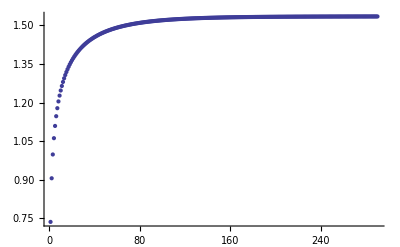

```mathematica
ListPlot[ta]
```

```mathematica
the saturation constant is approximately
```

```mathematica
ta[[290,2]]
```

1.53491

```mathematica
cfunction=Table[{ta[[i,1]],ta[[i,1]](ta[[i+1,2]]-ta[[i,2]])},{i,1,Length[ta]-1}];
```

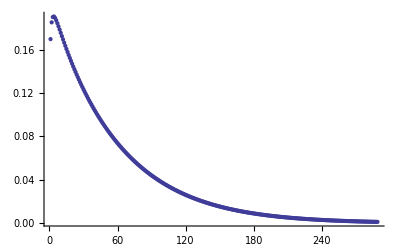

```mathematica
ListPlot[cfunction]
```

```mathematica
xxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxx
```

```mathematica
Now i try with a larger mass to see the mass dependence on the saturation constant
```

```mathematica
m=1/10;Rmax=40;
```

```mathematica
f=Table[NIntegrate[Exp[I x i]/4/Pi/Sqrt[m^2+2(1-Cos[x])],{x,-Pi,Pi}],{i,0,Rmax}];g=Table[NIntegrate[Exp[I x i]/4/Pi*Sqrt[m^2+2(1-Cos[x])],{x,-Pi,Pi}],{i,0,Rmax}];
```

```mathematica
entropy[40]
```

0.770144

```mathematica
then fitting , it gives the coefficient -1/3 in front of the log of the mass
```

```mathematica
Fit[{{1/10,0.7701438146581794},{1/100,1.534905060400002}},{1,Log[y]},y]
```

0.00538257-0.332132 Log[y]

```mathematica
xxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxx
```

```mathematica
Now i try with a very small mass to see how the 1/3Log[r] for the entropy is approached. I have to impruve numerical working precision a little bit
```

```mathematica
m=10^(-10);Rmax=40;
```

```mathematica
f=Table[NIntegrate[Exp[I x i]/4/Pi/Sqrt[m^2+2(1-Cos[x])],{x,-Pi,Pi}, WorkingPrecision->20,PrecisionGoal->10,MaxRecursion->20],{i,0,Rmax}];g=Table[NIntegrate[Exp[I x i]/4/Pi*Sqrt[m^2+2(1-Cos[x])],{x,-Pi,Pi}, WorkingPrecision->20,PrecisionGoal->10,MaxRecursion->20],{i,0,Rmax}];
```

```mathematica
cfunction=Table[{ta[[i,1]],ta[[i,1]](ta[[i+1,2]]-ta[[i,2]])},{i,1,Length[ta]-1}];
```

```mathematica
ta=Table[{R,entropy[R]},{R,1,40}];
```

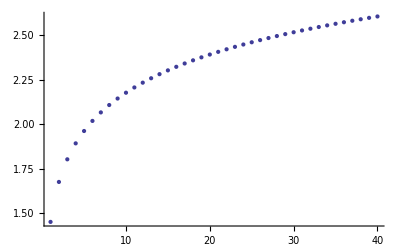

```mathematica
ListPlot[ta]
```

```mathematica
Fit[ta,{1,Log[y]},y]
```

1.4584152746293+0.31161045821781 Log[y]

```mathematica
still not 0.3333!
```